```mathematica
S=-N*k*((En/(N*e))*Log[En/(N*e)]+(1-En/(N*e))*Log[1-En/(N*e)])+k*(N-En/e)*Log[2];
```

```mathematica
D[S,En]//FullSimplify
```

(k (Log[1-En/(e N)]-Log[(2 En)/(e N)]))/e

```mathematica
Solve[1/T==(k (Log[1-En/(e N)]-Log[(2 En)/(e N)]))/e,En]
```

{{En→(e N)/(1+2 ⅇ^(e/(k T)))}}

```mathematica
HC=D[(e N)/(1+2 ⅇ^(e/(k T))),T]//FullSimplify
```

(2 e^2 ⅇ^(e/(k T)) N)/(k (T+2 ⅇ^(e/(k T)) T)^2)

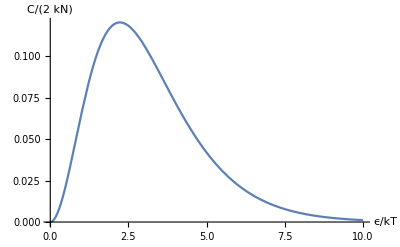

```mathematica
Plot[x^2*Exp[x]/(1+2*Exp[x])^2,{x,0,10},AxesLabel->{ϵ/kT,C/(2kN)}]
```

```mathematica
(*Schematic plot of E(T)*)
```

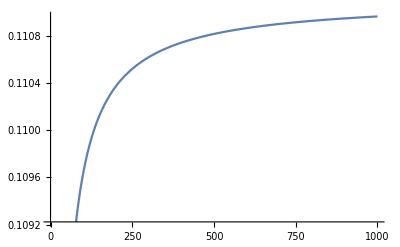

```mathematica
Plot[1/(1+2*Exp[1/T])^2,{T,0,1000}]
```

```mathematica
(*Find max E*)
```

```mathematica
Limit[(e N)/(1+2 ⅇ^(e/(k T))),T->Infinity]
```

(e N)/3